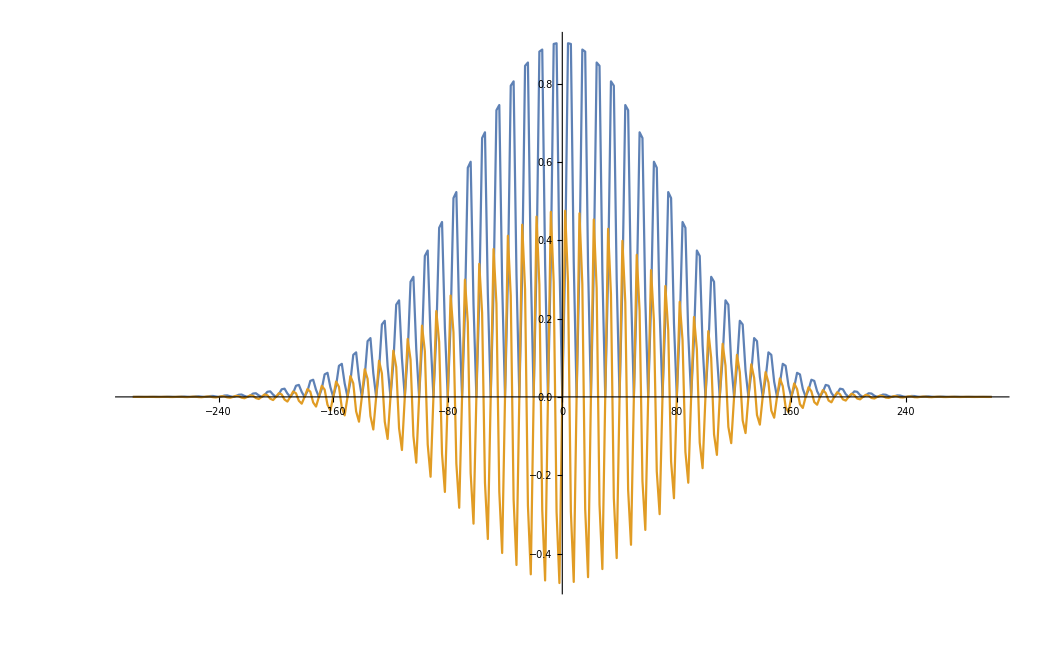

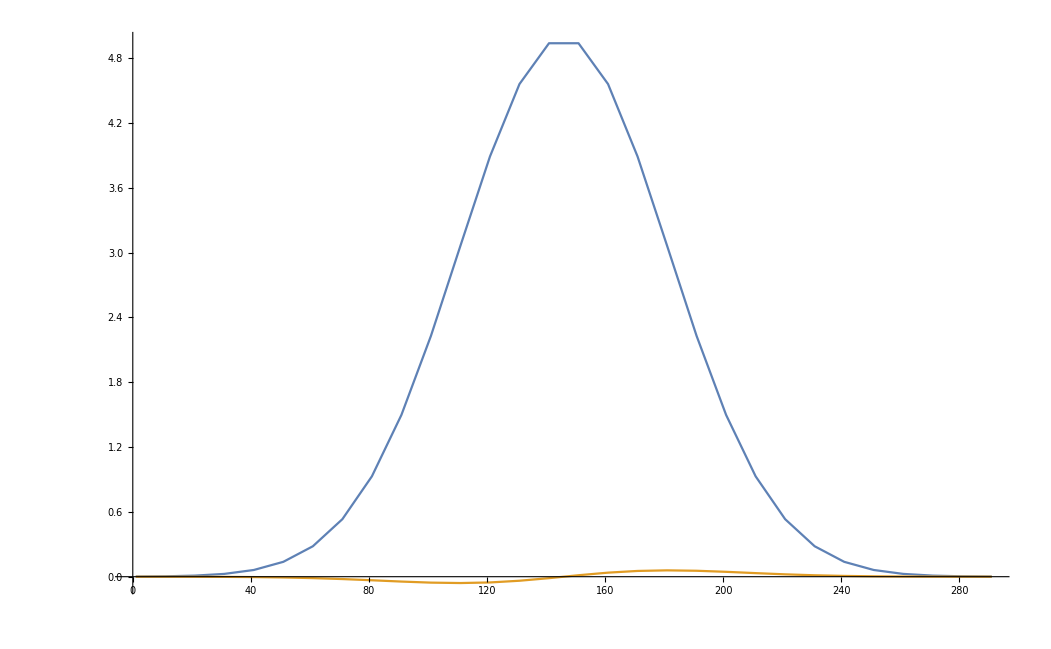

```mathematica
g[x_]:=Exp[-x^2/100^2];
S[x_]:=g[x]Sin[x π/10];
p=0.0;
SI[x_]:=S[x]Sin[x π/10+p];
SQ[x_]:=S[x]Cos[x π/10+p];
TSI=Table[{2i,SI[2 i]},{i,-150,150}];
TSQ=Table[{2i,SQ[2 i]},{i,-150,150}];
ListPlot[{TSI,TSQ},Joined->True,PlotRange->All]

SI1=Table[{j,Sum[TSI[[i,2]],{i,j,j+9}]},{j,1,295,10}];
SQ1=Table[{j,Sum[TSQ[[i,2]],{i,j,j+9}]},{j,1,295,10}];
ListPlot[{SI1,SQ1},Joined->True]
```